### Маятник

```mathematica
m=0.3;
k=20;
τ=0.01;
T=1;
EulerExplicitMx= Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Численные методы\\ODE\\Программа\\ODE\\Эйлер_явный_mx.txt","Table"];
EulerImplicitMx= Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Численные методы\\ODE\\Программа\\ODE\\Эйлер_неявный_mx.txt","Table"];
```

```mathematica
Analytical1 = DSolve[{m x''[t]==-k x[t],x[0]==1,x'[0]==0},x[t],t];
Analytical2 = DSolve[{x'[t]==y[t],y'[t]==-(k/m)x[t],x[0]==1,y[0]==0},{x[t],y[t]},t]
```

{{x[t]→(1.-6.16298×10^-33 ⅈ) ((1.+0. ⅈ) Cos[8.16497 t]+(1.12155×10^-18-9.3388×10^-35 ⅈ) Sin[8.16497 t]),y[t]→(-8.16497+1.83149×10^-17 ⅈ) ((0.+0. ⅈ)+(1.+0. ⅈ) Sin[8.16497 t])}}

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.First[Analytical2]],{t,0,T}]
```

-Graphics-

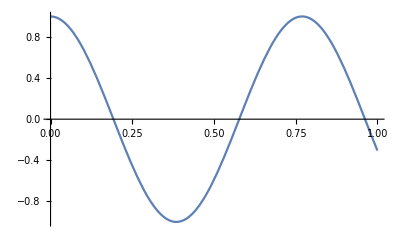

```mathematica
Plot[Evaluate[x[t]/.First[Analytical1]],{t,0,T}]
```

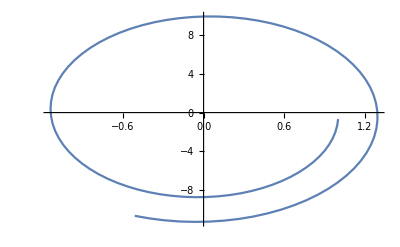

```mathematica
ListLinePlot[EulerExplicitMx]
```

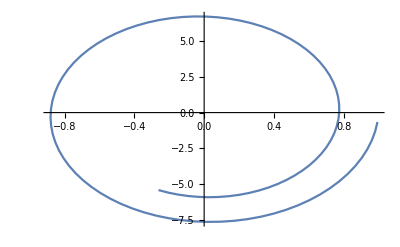

```mathematica
ListLinePlot[EulerImplicitMx]
```

### Пример 1

```mathematica
Euler= Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Численные методы\\ODE\\Программа\\ODE\\Эйлер.txt","Table"];
RK4= Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Численные методы\\ODE\\Программа\\ODE\\Рунге-Кутта.txt","Table"];
Adams= Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Численные методы\\ODE\\Программа\\ODE\\Адамс.txt","Table"];
PEC= Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Численные методы\\ODE\\Программа\\ODE\\Прогноз-коррекция.txt","Table"];
```

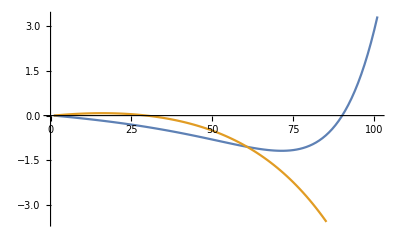

```mathematica
ListLinePlot[Transpose@Euler]
```

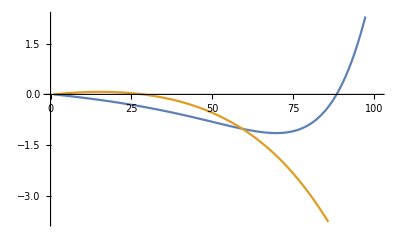

```mathematica
ListLinePlot[Transpose@RK4]
```

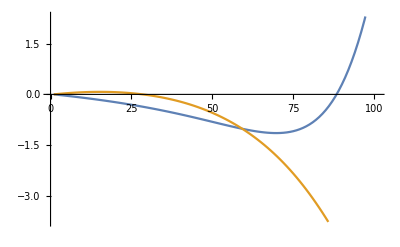

```mathematica
ListLinePlot[Transpose@Adams]
```

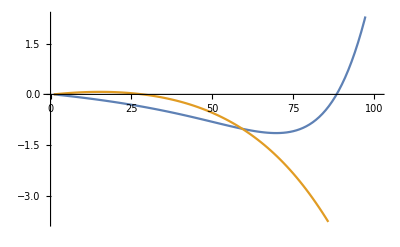

```mathematica
ListLinePlot[Transpose@PEC]
```

## Вариант 1

```mathematica
DSolve[{x'[t]==y[t],y'[t]==2*0.3*y[t]*(1.0-1.0*(x^2)[t])-1.0^2 x[t],x[0] ==0.1,y[0]==0.1 },{x,y},t]
```

DSolve::dvnoarg: The function x appears with no arguments.

DSolve[{x'[t]==y[t],y'[t]==-1. x[t]+0.6 (1.-1. x^2[t]) y[t],x[0]==0.1,y[0]==0.1},{x,y},t]